## Fixed M_Z'=10 TeV, Fixed Brane parameter = 1, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 ( (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime10=10;
MassNu=0.1;
CvL1=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(1.0)
```

0.999871

```mathematica
Zprime10decayfixedmass1[CvR_]:=MassZprime10/(12π)(1/4(CvL1+CvR)^2+1/4(CvL1-CvR)^2+2(MassNu/MassZprime10)^2(1/4(CvL1+CvR)^2-1/2(CvL1+CvR)^2))√(1-4(MassNu/MassZprime10)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime10decayfixedmass1Table=Table[{Q[i],Zprime10decayfixedmass1[Q[i]]},{i,0,Npt}]
```

{{0.,132.555},{0.1,133.878},{0.2,137.853},{0.3,144.48},{0.4,153.759},{0.5,165.689},{0.6,180.271},{0.7,197.505},{0.8,217.391},{0.9,239.929},{1.,265.118}}

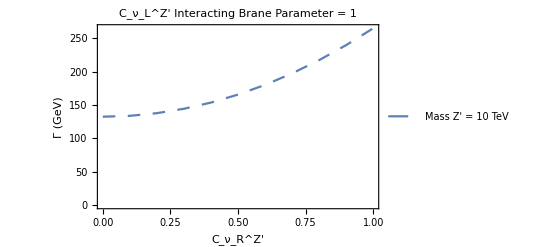

```mathematica
PlotZprimeDecayFixed101=ListPlot[%, Joined-> True,PlotStyle->{Dashing[Medium]},PlotLegends->{"Mass Z' = 10 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm["C_ν_L^Z'  Interacting Brane Parameter = 1"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

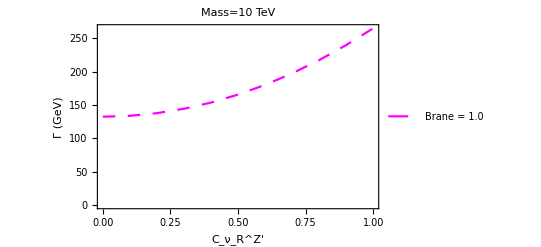

```mathematica
PlotZprimeDecayFixed101B=ListPlot[%%, Joined-> True,PlotStyle->{Magenta,Dashing[Medium]},PlotLegends->{"Brane = 1.0"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 10 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime10decayfixedmass1Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 132.555
0.1 | 133.878
0.2 | 137.853
0.3 | 144.48
0.4 | 153.759
0.5 | 165.689
0.6 | 180.271
0.7 | 197.505
0.8 | 217.391
0.9 | 239.929
1. | 265.118

## Fixed M_Z'=8 TeV, Fixed Brane parameter = 1, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime8=8;
MassNu=0.1;
CvL1=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(1.0)
```

0.999871

```mathematica
Zprime8decayfixedmass1[CvR_]:=MassZprime8/(12π)(1/4(CvL1+CvR)^2+1/4(CvL1-CvR)^2+2(MassNu/MassZprime8)^2(1/4(CvL1+CvR)^2-1/2(CvL1+CvR)^2))√(1-4(MassNu/MassZprime8)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime8decayfixedmass1Table=Table[{Q[i],Zprime8decayfixedmass1[Q[i]]},{i,0,Npt}]
```

{{0.,106.026},{0.1,107.083},{0.2,110.262},{0.3,115.561},{0.4,122.982},{0.5,132.523},{0.6,144.186},{0.7,157.969},{0.8,173.874},{0.9,191.9},{1.,212.047}}

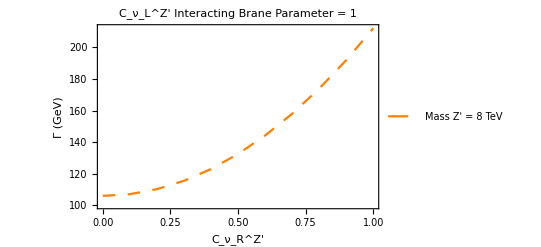

```mathematica
PlotZprimeDecayFixed81=ListPlot[%, Joined-> True,PlotStyle->{Orange, Dashing[Medium]},PlotLegends->{"Mass Z' = 8 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm["C_ν_L^Z' Interacting Brane Parameter = 1"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

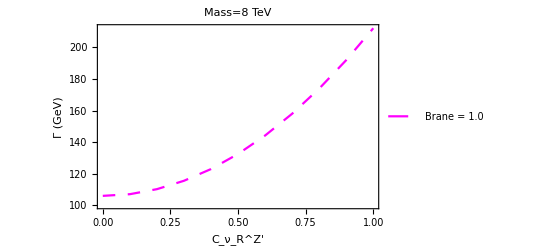

```mathematica
PlotZprimeDecayFixed81B=ListPlot[%%, Joined-> True,PlotStyle->{Magenta,Dashing[Medium]},PlotLegends->{"Brane = 1.0"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 8 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime8decayfixedmass1Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 106.026
0.1 | 107.083
0.2 | 110.262
0.3 | 115.561
0.4 | 122.982
0.5 | 132.523
0.6 | 144.186
0.7 | 157.969
0.8 | 173.874
0.9 | 191.9
1. | 212.047

## Fixed M_Z'=5 TeV, Fixed Brane parameter = 1, Vary parameter C_ν_Ri^Z'

Γ (Z'→ν ν̄) =  (g_PQ^2 M_(Z '))/(12π) ((1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2+(1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2+2 m_ν^2/(M_(Z ')^2) (  (1/2(C_ν_Li^(Z ')+C_ν_Ri^(Z ')))^2-2 (1/2(C_ν_Li^(Z ')-C_ν_Ri^(Z ')))^2 )√(1-4 m_ν^2/M_Z'^2)

```mathematica
MassZprime5=5;
MassNu=0.1;
CvL1=-1/4(e^2/(sinsquared(1-sinsquared)))(0.001)+(1.0)
```

0.999871

```mathematica
Zprime5decayfixedmass1[CvR_]:=MassZprime5/(12π)(1/4(CvL1+CvR)^2+1/4(CvL1-CvR)^2+2(MassNu/MassZprime5)^2(1/4(CvL1+CvR)^2-1/2(CvL1+CvR)^2))√(1-4(MassNu/MassZprime5)^2)*10^3
Qmax=1.0;
Qmin=0.0;
Npt=10;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
Zprime5decayfixedmass1Table=Table[{Q[i],Zprime5decayfixedmass1[Q[i]]},{i,0,Npt}]
```

{{0.,66.2179},{0.1,66.8749},{0.2,68.8567},{0.3,72.1631},{0.4,76.7943},{0.5,82.7501},{0.6,90.0307},{0.7,98.6359},{0.8,108.566},{0.9,119.821},{1.,132.4}}

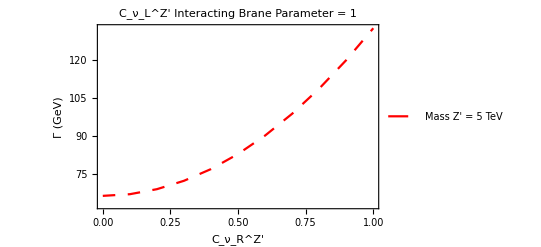

```mathematica
PlotZprimeDecayFixed51=ListPlot[%, Joined-> True,PlotStyle->{Red, Dashing[Medium]},PlotLegends->{"Mass Z' = 5 TeV"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm["C_ν_L^Z'  Interacting Brane Parameter = 1"],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

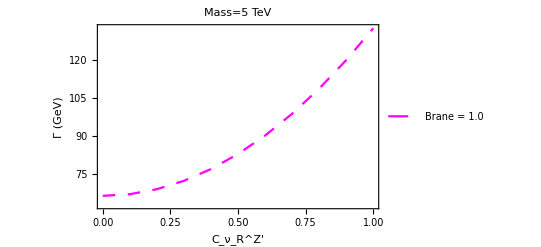

```mathematica
PlotZprimeDecayFixed51B=ListPlot[%%, Joined-> True,PlotStyle->{Magenta,Dashing[Medium]},PlotLegends->{"Brane = 1.0"},Frame->True,FrameLabel->{"C_ν_R^Z'","Γ (GeV)"},PlotLabel->HoldForm[Mass = 5 TeV],LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}]
```

```mathematica
TableForm[Zprime5decayfixedmass1Table,TableHeadings-> {None,{"CvR","Decay Rate(GeV)"}}]
```

CvR | Decay Rate(GeV)
0. | 66.2179
0.1 | 66.8749
0.2 | 68.8567
0.3 | 72.1631
0.4 | 76.7943
0.5 | 82.7501
0.6 | 90.0307
0.7 | 98.6359
0.8 | 108.566
0.9 | 119.821
1. | 132.4

## OverLay

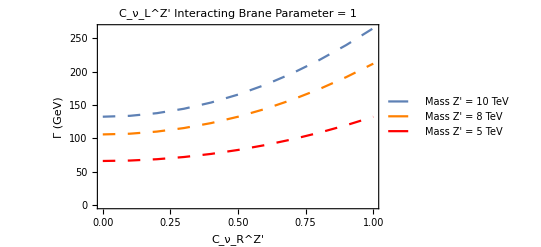

```mathematica
Show[PlotZprimeDecayFixed101,PlotZprimeDecayFixed81,PlotZprimeDecayFixed51]
```

## OverLay 2

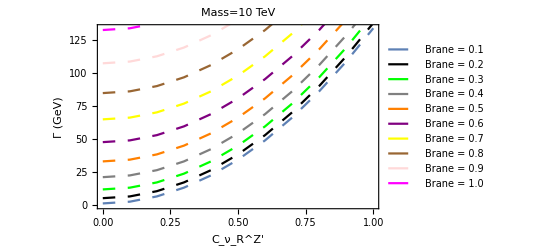

```mathematica
Show[PlotZprimeDecayFixed1001B,PlotZprimeDecayFixed1002B,PlotZprimeDecayFixed1003B,PlotZprimeDecayFixed1004B,PlotZprimeDecayFixed1005B,PlotZprimeDecayFixed1006B,PlotZprimeDecayFixed1007B,PlotZprimeDecayFixed1008B,PlotZprimeDecayFixed1009B,PlotZprimeDecayFixed101B]
```

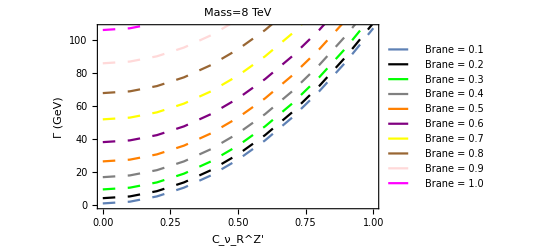

```mathematica
Show[PlotZprimeDecayFixed801B,PlotZprimeDecayFixed802B,PlotZprimeDecayFixed803B,PlotZprimeDecayFixed804B,PlotZprimeDecayFixed805B,PlotZprimeDecayFixed806B,PlotZprimeDecayFixed807B,PlotZprimeDecayFixed808B,PlotZprimeDecayFixed809B,PlotZprimeDecayFixed81B]
```

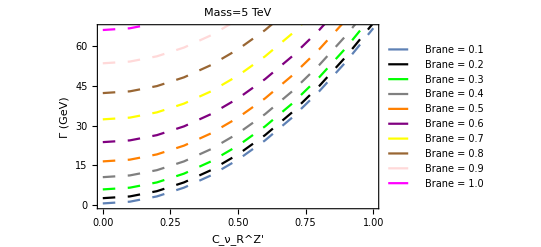

```mathematica
Show[PlotZprimeDecayFixed501B,PlotZprimeDecayFixed502B,PlotZprimeDecayFixed503B,PlotZprimeDecayFixed504B,PlotZprimeDecayFixed505B,PlotZprimeDecayFixed506B,PlotZprimeDecayFixed507B,PlotZprimeDecayFixed508B,PlotZprimeDecayFixed509B,PlotZprimeDecayFixed51B]
```